```mathematica
Plot3D[(1+β(1-β)(n-1))/(1+(1-β)(n-1)),{n,1,2},{β,-1,1},PlotRange->{{1,2},{-1,1},{0,1}},AxesLabel->{"Refraction index","Speed of matter (positive in direction of light)","Speed of light"},ImageSize->{720,480}]
```

-Graphics3D-

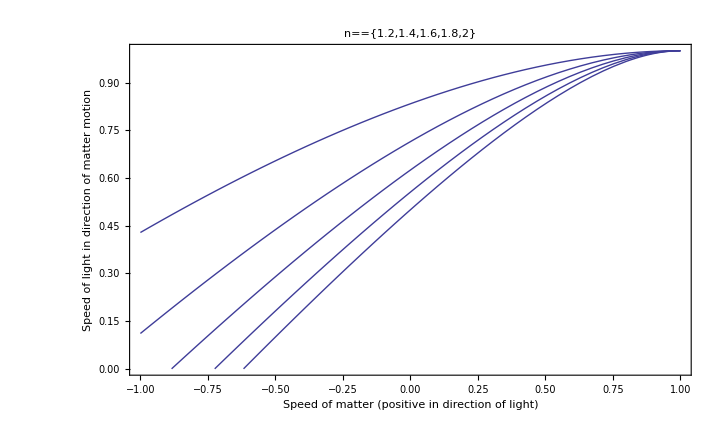

```mathematica
Plot[(1+β(1-β)(n-1))/(1+(1-β)(n-1))/.n->{1.2,1.4,1.6,1.8,2},{β,-1,1},Axes->False,Frame->True,FrameLabel->{"Speed of matter (positive in direction of light)","Speed of light in direction of matter motion"},PlotLabel->n=={1.2,1.4,1.6,1.8,2},PlotRange->{{-1,1},{0,1}}]
```

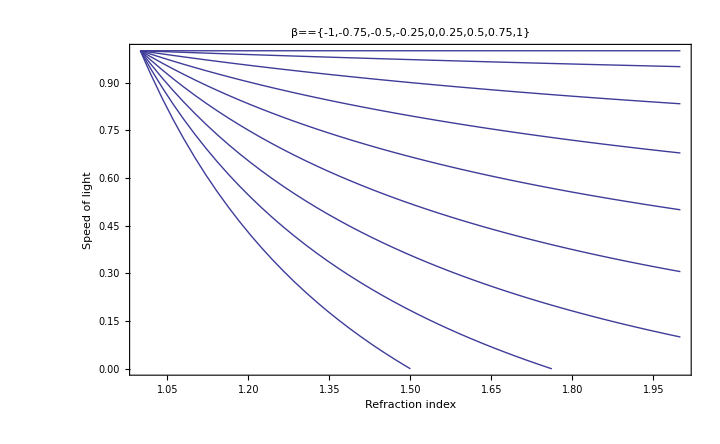

```mathematica
Plot[(1+β(1-β)(n-1))/(1+(1-β)(n-1))/.β->{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1},{n,1,2},Axes->False,Frame->True,FrameLabel->{"Refraction index","Speed of light"},ImageSize->{720,480},PlotRange->{{1,2},{0,1}},PlotLabel->β=={-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}]
```

```mathematica
Solve[(1+β(1-β)(n-1))/(1+(1-β)(n-1))==0,β]//FullSimplify
```

{{β→(1-n+√((-1+n) (3+n)))/(2-2 n)},{β→(-1+n+√((-1+n) (3+n)))/(2 (-1+n))}}

```mathematica
%29/.n->2.
```

{{β→-0.618034},{β→1.61803}}

```mathematica
При малых скоростях материи применимо приближение β'=1/n+β(1-n^-2)
```